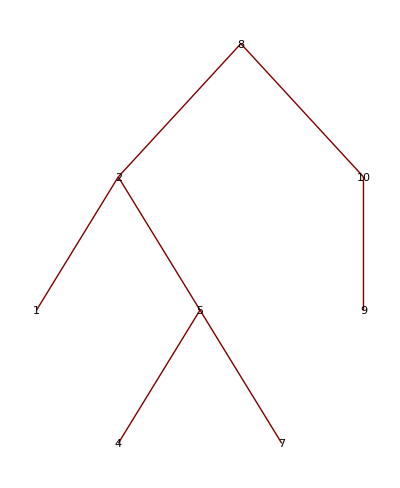

```mathematica
tree = {8->2, 2->1, 2->5, 5->4, 5->7, 8->10, 10->9};
TreePlot[tree,Top, 8,VertexLabeling->True]
```

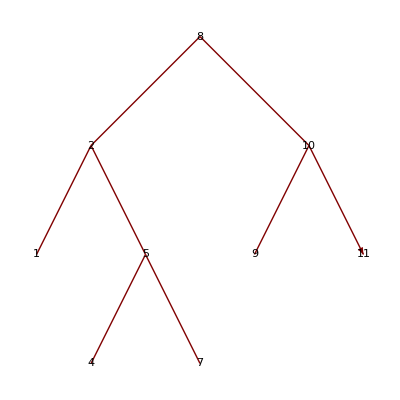

```mathematica
Show[%34,PlotLabel->None,LabelStyle->{25,GrayLevel[0],Bold}]
```

```mathematica
maybeP=Except[nothing]|nothing
binaryTreeNodeP={Except[nothing],maybeP,maybeP}

childOrEmptyNode[value:Except[nothing],nothing,side:(left|right)]:="empty"<>ToString[value]<>ToString[side]
childOrEmptyNode[Except[nothing],child:Except[Nothing],(left|right)]:=child

binaryTreeNodeEdges[{v:Except[nothing],l:maybeP,r:maybeP}]:={v->childOrEmptyNode[v,l,left],v->childOrEmptyNode[v,r,right]}
makeBinaryTree[nodes:{binaryTreeNodeP..}]:=Flatten[Map[binaryTreeNodeEdges,nodes]]

removeEmptyEdges=(If[!StringMatchQ[ToString[#2[[2]]],"empty"~~__],{Darker[Red],Arrowheads[{{Medium,0.5}}],Arrow[#1]}]&)
removeEmptyVertices=(If[!StringMatchQ[ToString[#2],"empty"~~__],{Background->LightYellow,Inset[Framed[#2],#1]}]&)
```

Except[nothing]|nothing

{Except[nothing],Except[nothing]|nothing,Except[nothing]|nothing}

If[!StringMatchQ[ToString[#2⟦2⟧],empty~~__],{Darker[Red],Arrowheads[{{Medium,0.5}}],Arrow[#1]}]&

If[!StringMatchQ[ToString[#2],empty~~__],{Background→LightYellow,Inset[#2,#1]}]&

{{8,2,10},{2,1,5},{5,4,6},{10,9,nothing}}

{{6,2,10},{2,1,5},{5,4,nothing},{10,9,nothing}}

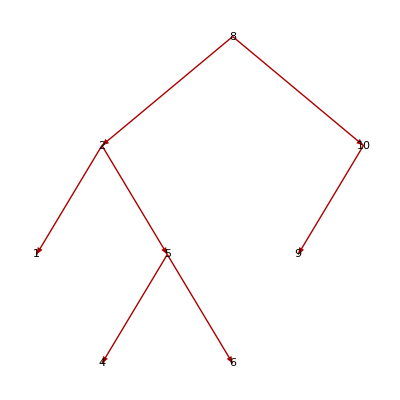

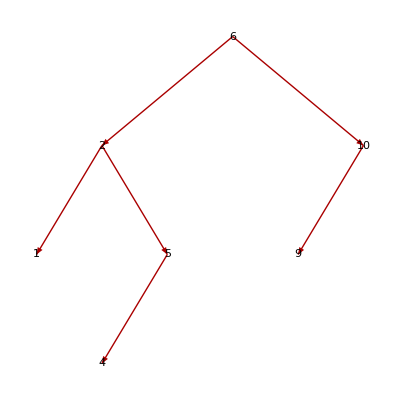

```mathematica
nodes1={{8, 2, 10},{2,1,5},{5, 4, 6},{10,9,nothing}}
nodes2={{6, 2, 10},{2,1,5},{5, 4, nothing},{10,9,nothing}}
plot1 =TreePlot[makeBinaryTree[nodes1],Top,8,VertexRenderingFunction->removeEmptyVertices,EdgeRenderingFunction->removeEmptyEdges]
plot2 =TreePlot[makeBinaryTree[nodes2],Top,6,VertexRenderingFunction->removeEmptyVertices,EdgeRenderingFunction->removeEmptyEdges]
```

```mathematica
Export[ "f:\\Users\\Andrea\\Documents\\baeldung\\binary-tree-1.gif", plot1, ImageSize->400, ImageResolution->300]
```

f:\Users\Andrea\Documents\baeldung\binary-tree-1.gif

```mathematica
Export[ "f:\\Users\\Andrea\\Documents\\baeldung\\binary-tree-2.gif", plot2, ImageSize->400, ImageResolution->300]
```

f:\Users\Andrea\Documents\baeldung\binary-tree-2.gif

```mathematica
SystemOpen["f:\\Users\\Andrea\\Documents\\baeldung\\binary-tree-2.gif"]
```

```mathematica
SystemOpen["f:\\Users\\Andrea\\Documents\\baeldung\\binary-tree-1.gif"]
```

```mathematica
SystemOpen["f:\\Users\\Andrea\\Documents\\baeldung\\binary-tree-1.gif"]
```

```mathematica
SystemOpen["f:\\Users\\Andrea\\Documents\\baeldung\\binary-tree-1.gif"]
```

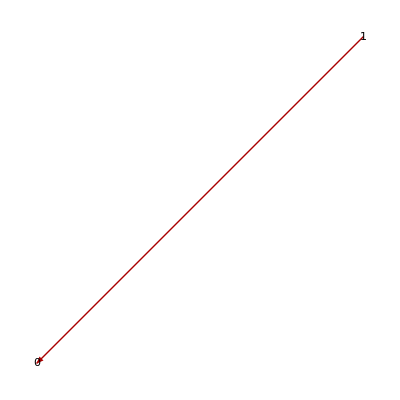

f:\Users\Andrea\Documents\baeldung\binary-tree-3.gif

```mathematica
plot3 = TreePlot[makeBinaryTree[{{1, 0, nothing}}],Top,1,VertexRenderingFunction->removeEmptyVertices,EdgeRenderingFunction->removeEmptyEdges]
Export[ "f:\\Users\\Andrea\\Documents\\baeldung\\binary-tree-3.gif", plot3, ImageSize->400, ImageResolution->300]
```

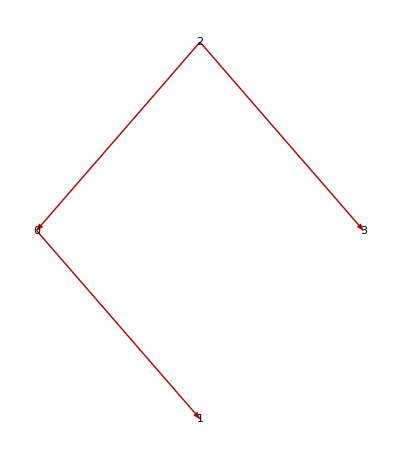

f:\Users\Andrea\Documents\baeldung\binary-tree-4.gif

```mathematica
plot4 = TreePlot[makeBinaryTree[{{2, 0, 3}, {0, nothing, 1}}],Top,2,VertexRenderingFunction->removeEmptyVertices,EdgeRenderingFunction->removeEmptyEdges]
Export[ "f:\\Users\\Andrea\\Documents\\baeldung\\binary-tree-4.gif", plot4, ImageSize->400, ImageResolution->300]
```